```mathematica
especies= 15;
metabolitos= 22;
```

```mathematica
n=especies;
m=metabolitos;
```

```mathematica
H = Table[RandomReal[{0.1,1}],m];
μ = Table[RandomReal[{0.01,0.1}],m];
δ = Table[RandomReal[{0.01,0.1}],n];
S = Table[RandomReal[5],m];
ciC = Table[RandomReal[5],m];
ciX = Table[RandomReal[5],n];
```

```mathematica
V = {
	{0,0,0,0,0,0,0,0,0,RandomReal[1],0,RandomReal[1],RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,RandomReal[1],0,0,0,0,0,RandomReal[1],0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,RandomReal[1],RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,RandomReal[1],0,0,0,0,RandomReal[1],0},
	{0,0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,RandomReal[1],0,RandomReal[1],0,0,0},
	{0,0,0,RandomReal[1],0,0,0,0,0,RandomReal[1],0,0,0,0,0},
	{RandomReal[1],0,0,0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,RandomReal[1],0,0,0,0,0,RandomReal[1],0,0,0,0,RandomReal[1],0},
	{0,0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,RandomReal[1]},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0,0},
	{0,0,0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,RandomReal[1],0,0,RandomReal[1],0},
	{0,0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,0,0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0}
	};
W = {
	{RandomReal[1],0,RandomReal[1],RandomReal[1],0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,RandomReal[1],0,0,RandomReal[1],RandomReal[1]},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,RandomReal[1],0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,RandomReal[1],0,RandomReal[1],RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,0,RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{RandomReal[1],0,RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0,0},
	{0,0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1]},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
};
```

```mathematica
V//MatrixForm;
```

```mathematica
W//MatrixForm;
```

```mathematica
concentrationsGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["c"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
speciesGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["x"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
G[c_, v_] := v.c
```

```mathematica
R[i_]:= (c[t]⟦i⟧)/(H⟦i⟧+c[t]⟦i⟧)
```

```mathematica
c[t_]=concentrationsGen[m];
x[t_] = speciesGen[n];
```

```mathematica
vars[t_]=Flatten[{c[t],x[t]}];
```

```mathematica
g =Table[ G[V⟦;;,i⟧,c[t]],{i,1,n}];
```

```mathematica
r = Table[R[i],{i,1,m}];
```

```mathematica
eqC = Table[c'[t]⟦i⟧==S⟦i⟧ +( W.x[t])⟦i⟧ r⟦i⟧-(V.x[t])⟦i⟧r⟦i⟧-(μ⟦i⟧c[t]⟦i⟧),{i,1,Length[c[t]]}];
eqX = Table[x'[t]⟦i⟧==x[t]⟦i⟧(g⟦i⟧-δ⟦i⟧),{i,1,Length[x[t]]}];
cisC = Table[c[0]⟦i⟧==ciC⟦i⟧,{i,1,Length[c[t]]}];
cisX = Table[x[0]⟦i⟧==ciX⟦i⟧,{i,1,Length[x[t]]}];
```

```mathematica
sistema = Flatten[{eqC,eqX,cisX,cisC}];
```

```mathematica
sol=NDSolve[sistema,vars[t],{t,0,100}];
```

```mathematica
varc[t_]=Flatten[{c[t]}];
varx[t_] =Flatten[{x[t]}];
```

```mathematica
prueba=NDSolve[sistema, varc[t],{t,0,100}];
try= NDSolve[sistema, varx[t],{t,0,100}];
```

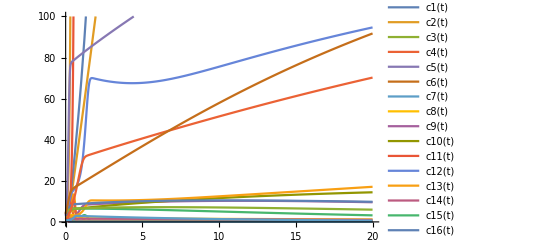

```mathematica
Plot[Evaluate[vars[t]/.sol],{t,0,20},PlotLegends->vars[t],PlotRange->{0,100}]
```

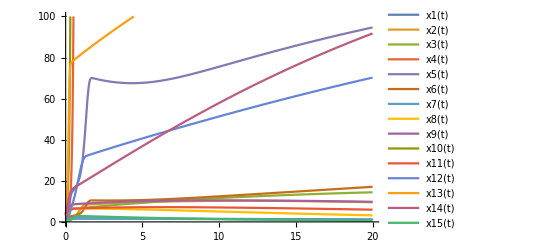

```mathematica
Plot[Evaluate[varx[t]/.try],{t,0,20},PlotLegends->varx[t],PlotRange->{0,100}]
```

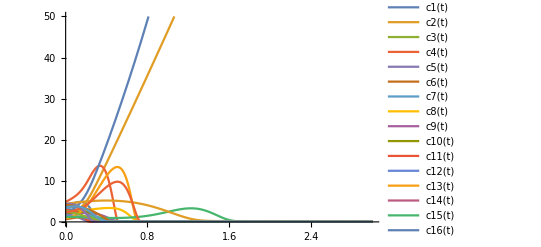

```mathematica
Plot[Evaluate[varc[t]/.prueba],{t,0,3},PlotLegends->varc[t],PlotRange->{0,50}]
```